```mathematica
x=RandomReal[1,{4,2}];
x={{0,0},{100.,0},{100,100}};
x=RandomReal[1,{4,2}];
x=Map[(#-Mean[x])&,x];
n=Length[x];
```

```mathematica
x
```

{{-0.058815,0.338262},{-0.291965,-0.278433},{0.237149,-0.359586},{0.113631,0.299758}}

```mathematica
(* square distance matrix *)
```

```mathematica
d=Table[Norm[x[[i]]-x[[j]]]*Norm[x[[i]]-x[[j]]],{i,n},{j,n}]
```

{{0.,0.434672,0.574586,0.0312202},{0.434672,0.,0.286548,0.498813},{0.574586,0.286548,0.,0.449991},{0.0312202,0.498813,0.449991,0.}}

```mathematica
(* double centered square distance matrix *)
```

```mathematica
A=-Table[d[[i,j]]-1/n*Sum[d[[k,j]],{k,1,n}]-1/n*Sum[d[[i,k]],{k,1,n}]+1/n/n*Sum[d[[k,l]],{k,n},{l,n}],{i,n},{j,n}]/2
```

{{0.11788,-0.0770113,-0.135582,0.0947133},{-0.0770113,0.162769,0.0308814,-0.116639},{-0.135582,0.0308814,0.185542,-0.0808411},{0.0947133,-0.116639,-0.0808411,0.102767}}

```mathematica
(* classical MDS *)
{dd1,B1}=Chop[Eigensystem[A]];
Print[{dd1,B1}];
x2=Transpose[Take[B1,2]].DiagonalMatrix[Sqrt[Take[dd1,2]]]
```

{{0.411512,0.157446,0,0},{{-0.523202,0.45195,0.545265,-0.474012},{-0.182306,-0.707067,0.633537,0.255836},{0.0210949,0.531408,0.275825,0.800676},{-0.817047,-0.0255512,-0.421961,0.392084}}}

{{-0.33563,-0.0723379},{0.289922,-0.28056},{0.349783,0.251384},{-0.304075,0.101514}}

```mathematica
(* pivot MDS. Distance to k center*)
```

```mathematica
k=3;
A2=Transpose[Take[A,k]]
```

{{0.11788,-0.0770113,-0.135582},{-0.0770113,0.162769,0.0308814},{-0.135582,0.0308814,0.185542},{0.0947133,-0.116639,-0.0808411}}

```mathematica
(* egen vec of A2^T.A2 is v, then A2.v also eigen vec of A2.A2^T*)
```

```mathematica
{dd,B}=Chop[Eigensystem[Transpose[A2].A2]]
```

{{0.131861,0.0225987,0},{{0.597073,-0.488734,-0.636116},{-0.0871789,-0.827813,0.554189},{-0.797436,-0.275435,-0.536872}}}

```mathematica
A2v=A2.Transpose[B](*A2.v*)
```

{{0.194267,-0.0216637,0.},{-0.145176,-0.110914,-4.16334×10^-17},{-0.214071,0.0890811,1.38778×10^-17},{0.16498,0.0434969,-1.38778×10^-17}}

Very important : normalize!

```mathematica
(* normalize*)
A2v=Transpose[Map[(#/Norm[#])&,Transpose[A2v]]]
```

{{0.534984,-0.144109,0.},{-0.399795,-0.737812,-0.904534},{-0.589523,0.592576,0.301511},{0.454333,0.289345,-0.301511}}

```mathematica
(* check that these are indeed eigenvectors of A2.A2^T*)
{((A2.Transpose[A2]).A2v),A2v}
```

{{{0.0705434,-0.00325668,0.000836881},{-0.0527173,-0.0166736,-0.0151241},{-0.0777349,0.0133914,0.00651618},{0.0599087,0.00653883,0.00777104}},{{0.534984,-0.144109,0.},{-0.399795,-0.737812,-0.904534},{-0.589523,0.592576,0.301511},{0.454333,0.289345,-0.301511}}}

```mathematica
(* But may not be the eigevector of A*)
```

```mathematica
{(A.A2v)//MatrixForm,A2v//MatrixForm}
```

{(0.216813 | -0.0131055 | 0.000222725
-0.177472 | -0.124444 | -0.102751
-0.23099 | 0.0833105 | 0.0523842
0.19165 | 0.054239 | 0.050144),(0.534984 | -0.144109 | 0.
-0.399795 | -0.737812 | -0.904534
-0.589523 | 0.592576 | 0.301511
0.454333 | 0.289345 | -0.301511)}

```mathematica
x3=Map[Take[#,2]&,(A2v).DiagonalMatrix[Sqrt[Sqrt[dd]]]]
```

{{0.322381,-0.0558743},{-0.240916,-0.286066},{-0.355246,0.229755},{0.273781,0.112186}}

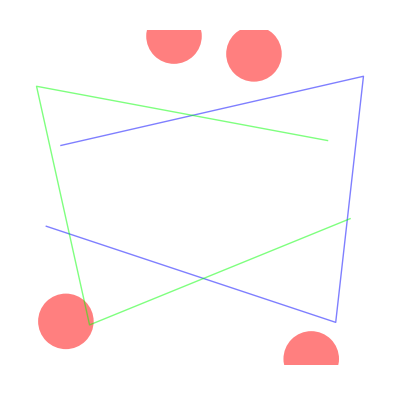

```mathematica
Graphics[{PointSize[.1],RGBColor[1,0,0,.5],Point[x],RGBColor[0,0,1,.5],Line[x2],RGBColor[0,1,0,.5], Line[x3]}]
```